2016
This program calculates the integrands of Feynman integrals, and related quantities, of one-photon-to-three-photon process, at one-loop level.
It is shown that the related amplitude vanishes because of a kinematic constraint (that the final state photons must be collinear with the initial state photon). 

Modified from 3-photon 1-loop example given in FeynCalc documentation.

This software is covered by the GNU General Public License 3. Copyright (C) 
1990-2016 Rolf Mertig, 1997-2016 Frederik Orellana, 2014-2016 Vladyslav Shtabovenko

First, load FeynCalc Package, if not already loaded.

#### 0. FeynCalc package

```mathematica
ClearAll;
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;];
$LoadFeynArts=True;
(*$LoadAddOns={"FeynHelpers"};*)
<<FeynCalc`
$FAVerbose=0;
```

FeynCalc 9.1.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.9 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

#### 1. Create Feynman diagrams

1.1. The graphs are contained in FeynDiags.

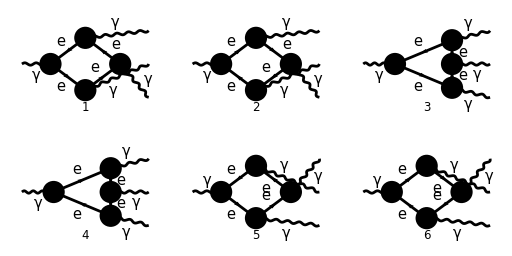

```mathematica
Paint[
FeynDiags=InsertFields[
CreateTopologies[1,1->3],
{V[1]}->{V[1],V[1],V[1]},
InsertionLevel->{Particles},
GenericModel->"Lorentz",
Model->"SMQCD",
ExcludeParticles->{S[1],S[2],S[3],V[2],V[3],F[3],F[4],U[1],U[2],U[3],U[4],F[2,{2}],F[2,{3}]}
],
ColumnsXRows->{3,2},
SheetHeader->False,
Numbering->Simple,
ImageSize->{512,256}
];
```

1.2. An example that shows how to plot (or otherwise call) a single graph:
Take[FeynDiags,{index}], where index chooses which graph to take.
Note: a single index contains two graph with opposite internal momentum.

#### 2. Generate feynman amplitude (feynman integral)

Some words on the used notation. 
Feynman integral is the loop-integral over internal momentum (in one-loop cases), 
i.e. the Feynman amplitude without the overall-momentum conserving delta function 
and the state factors (spinors for fermions, polarization vectors for photons). 
In case the external particles are all bosons, the feynman integrand is actually a tensor. 

In the output, the overall momentum conservation is not written explicitly.
Neither is the final loop-momentum integral factor ∫ d^4 q (the output is the integrand 
of the feynman amplitude). Note that the prefactor 1/(2π)^4is included in the output. 
Finally, the bosonic state factors (polarization vectors for photons, spinors for fermions) 
are not written explicitly in the output.

```mathematica
FeynInt=FCFAConvert[
CreateFeynAmp[
FeynDiags,
Truncated->True,
GaugeRules->{}],
IncomingMomenta->{k1},
OutgoingMomenta->{k2,k3,k4},
LoopMomenta->{q},
UndoChiralSplittings->True,
List->False,
SMP->True
];
```

```mathematica
FeynInt//Simplify
```

1/(16 π^4)ⅈ ((tr((γ̄·(-OverBar[k2]-OverBar[k3]-OverBar[k4]+q̄)+m_e).(-ⅈ e (γ̄)^Lor4).(γ̄·(-OverBar[k2]-OverBar[k3]+q̄)+m_e).(-ⅈ e (γ̄)^Lor3).(γ̄·(q̄-OverBar[k2])+m_e).(-ⅈ e (γ̄)^Lor2).(γ̄·q̄+m_e).(-ⅈ e (γ̄)^Lor1)))/((q^2-m_e^2).((q-k2)^2-m_e^2).((-k2-k3+q)^2-m_e^2).((-k2-k3-k4+q)^2-m_e^2))+(tr((γ̄·(-OverBar[k2]-OverBar[k3]-OverBar[k4]+q̄)+m_e).(ⅈ e (γ̄)^Lor4).(γ̄·(-OverBar[k2]-OverBar[k3]+q̄)+m_e).(ⅈ e (γ̄)^Lor3).(γ̄·(q̄-OverBar[k2])+m_e).(ⅈ e (γ̄)^Lor2).(γ̄·q̄+m_e).(ⅈ e (γ̄)^Lor1)))/((q^2-m_e^2).((q-k2)^2-m_e^2).((-k2-k3+q)^2-m_e^2).((-k2-k3-k4+q)^2-m_e^2))+(tr((m_e-γ̄·q̄).(-ⅈ e (γ̄)^Lor2).(γ̄·(OverBar[k2]-q̄)+m_e).(-ⅈ e (γ̄)^Lor4).(γ̄·(OverBar[k2]+OverBar[k4]-q̄)+m_e).(-ⅈ e (γ̄)^Lor3).(γ̄·(OverBar[k2]+OverBar[k3]+OverBar[k4]-q̄)+m_e).(-ⅈ e (γ̄)^Lor1)))/((q^2-m_e^2).((q-k2)^2-m_e^2).((-k2-k4+q)^2-m_e^2).((-k2-k3-k4+q)^2-m_e^2))+(tr((m_e-γ̄·q̄).(ⅈ e (γ̄)^Lor2).(γ̄·(OverBar[k2]-q̄)+m_e).(ⅈ e (γ̄)^Lor4).(γ̄·(OverBar[k2]+OverBar[k4]-q̄)+m_e).(ⅈ e (γ̄)^Lor3).(γ̄·(OverBar[k2]+OverBar[k3]+OverBar[k4]-q̄)+m_e).(ⅈ e (γ̄)^Lor1)))/((q^2-m_e^2).((q-k2)^2-m_e^2).((-k2-k4+q)^2-m_e^2).((-k2-k3-k4+q)^2-m_e^2))+(tr((γ̄·(-OverBar[k2]-OverBar[k3]-OverBar[k4]+q̄)+m_e).(-ⅈ e (γ̄)^Lor4).(γ̄·(-OverBar[k2]-OverBar[k3]+q̄)+m_e).(-ⅈ e (γ̄)^Lor2).(γ̄·(q̄-OverBar[k3])+m_e).(-ⅈ e (γ̄)^Lor3).(γ̄·q̄+m_e).(-ⅈ e (γ̄)^Lor1)))/((q^2-m_e^2).((q-k3)^2-m_e^2).((-k2-k3+q)^2-m_e^2).((-k2-k3-k4+q)^2-m_e^2))+(tr((γ̄·(-OverBar[k2]-OverBar[k3]-OverBar[k4]+q̄)+m_e).(ⅈ e (γ̄)^Lor4).(γ̄·(-OverBar[k2]-OverBar[k3]+q̄)+m_e).(ⅈ e (γ̄)^Lor2).(γ̄·(q̄-OverBar[k3])+m_e).(ⅈ e (γ̄)^Lor3).(γ̄·q̄+m_e).(ⅈ e (γ̄)^Lor1)))/((q^2-m_e^2).((q-k3)^2-m_e^2).((-k2-k3+q)^2-m_e^2).((-k2-k3-k4+q)^2-m_e^2)))

The expression agrees to what is obtained by hand.
The same result is also obtained as a sum of FeynInt1, FeynInt2 and FeynInt3.

3 Compute the trace:

```mathematica
FeynIntTraced=FeynInt/.DiracTrace-> Tr;
```

#### 4 Contract with polarization vectors

To make the resulting tensor integrand more familiar, I contract it with the polarization vectors ϵ1,ϵ2,ϵ3 and ϵ4.

```mathematica
PolContFeynInt=Contract[
FeynIntTraced FV[ϵ1,LorentzIndex[Lor1]]FV[ϵ2,LorentzIndex[Lor2]]FV[ϵ3,LorentzIndex[Lor3]]FV[ϵ4,LorentzIndex[Lor4]]];
```

For on-shell photons, the momenta of each are collinear, which means that all the scalar products with the four-momenta are zero.
Likewise, the scalar products with the polarization vectors, as well as polarization-momentum scalar products are zero, because on-shell photons are only transversally polarized. 

These constraints have to be applied again for FeynCalc, which gives them again in the loop integral.

```mathematica
ClearScalarProducts;
ScalarProduct[k1,k2]=0;
ScalarProduct[k1,k3]=0;
ScalarProduct[k1,k4]=0;
ScalarProduct[k2,k3]=0;
ScalarProduct[k2,k4]=0;
ScalarProduct[k3,k4]=0;
ScalarProduct[k1,k1]=0;
ScalarProduct[k2,k2]=0;
ScalarProduct[k3,k3]=0;
ScalarProduct[k4,k4]=0;

ScalarProduct[ϵ1,k1]=0;
ScalarProduct[ϵ1,k2]=0;
ScalarProduct[ϵ1,k3]=0;
ScalarProduct[ϵ1,k4]=0;
ScalarProduct[ϵ2,k1]=0;
ScalarProduct[ϵ2,k2]=0;
ScalarProduct[ϵ2,k3]=0;
ScalarProduct[ϵ2,k4]=0;
ScalarProduct[ϵ3,k1]=0;
ScalarProduct[ϵ3,k2]=0;
ScalarProduct[ϵ3,k3]=0;
ScalarProduct[ϵ3,k4]=0;
ScalarProduct[ϵ4,k1]=0;
ScalarProduct[ϵ4,k2]=0;
ScalarProduct[ϵ4,k3]=0;
ScalarProduct[ϵ4,k4]=0;
```

```mathematica
PolContFeynInt//Simplify
```

1/(2 π^4)ⅈ e^4 (((OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3]) m_e^4+(OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4]) m_e^4-(OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4]) m_e^4+2 (q̄·OverBar[ϵ2]) (q̄·OverBar[ϵ4]) (OverBar[ϵ1]·OverBar[ϵ3]) m_e^2+2 (q̄·OverBar[ϵ2]) (q̄·OverBar[ϵ3]) (OverBar[ϵ1]·OverBar[ϵ4]) m_e^2+2 (OverBar[k2]·q̄) (OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3]) m_e^2+3 (OverBar[k3]·q̄) (OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3]) m_e^2+(OverBar[k4]·q̄) (OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3]) m_e^2+2 (OverBar[k2]·q̄) (OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4]) m_e^2+3 (OverBar[k3]·q̄) (OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4]) m_e^2+(OverBar[k4]·q̄) (OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4]) m_e^2-2 (OverBar[k2]·q̄) (OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4]) m_e^2-3 (OverBar[k3]·q̄) (OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4]) m_e^2-(OverBar[k4]·q̄) (OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4]) m_e^2+4 (OverBar[k2]·q̄) (q̄·OverBar[ϵ2]) (q̄·OverBar[ϵ3]) (OverBar[ϵ1]·OverBar[ϵ4])+4 (OverBar[k3]·q̄) (q̄·OverBar[ϵ2]) (q̄·OverBar[ϵ3]) (OverBar[ϵ1]·OverBar[ϵ4])+4 (OverBar[k4]·q̄) (q̄·OverBar[ϵ2]) (q̄·OverBar[ϵ3]) (OverBar[ϵ1]·OverBar[ϵ4])+2 (OverBar[k3]·q̄)^2 (OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3])+2 (OverBar[k2]·q̄) (OverBar[k3]·q̄) (OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3])+2 (OverBar[k3]·q̄) (OverBar[k4]·q̄) (OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3])+2 (OverBar[k3]·q̄)^2 (OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4])+2 (OverBar[k2]·q̄) (OverBar[k3]·q̄) (OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4])+2 (OverBar[k3]·q̄) (OverBar[k4]·q̄) (OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4])-2 (OverBar[k3]·q̄)^2 (OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4])-2 (OverBar[k2]·q̄) (OverBar[k3]·q̄) (OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4])-2 (OverBar[k3]·q̄) (OverBar[k4]·q̄) (OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4])+(q̄)^4 ((OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3])+(OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4])-(OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4]))+2 (q̄·OverBar[ϵ1]) ((q̄·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3]) m_e^2+(q̄·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4]) m_e^2+4 (q̄·OverBar[ϵ2]) (q̄·OverBar[ϵ3]) (q̄·OverBar[ϵ4])-(q̄)^2 (q̄·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3])+2 (OverBar[k2]·q̄) (q̄·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4])-(q̄)^2 (q̄·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4])+2 (OverBar[k3]·q̄) ((q̄·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3])+(q̄·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4])))-(q̄)^2 (2 (q̄·OverBar[ϵ2]) ((q̄·OverBar[ϵ4]) (OverBar[ϵ1]·OverBar[ϵ3])+(q̄·OverBar[ϵ3]) (OverBar[ϵ1]·OverBar[ϵ4]))+((OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3])+(OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4])-(OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4])) (2 m_e^2+2 (OverBar[k2]·q̄)+3 (OverBar[k3]·q̄)+OverBar[k4]·q̄)))/(q^2-m_e^2).((q-k3)^2-m_e^2).((-k2-k3+q)^2-m_e^2).((-k2-k3-k4+q)^2-m_e^2)+((OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3]) m_e^4-(OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4]) m_e^4+(OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4]) m_e^4+2 (q̄·OverBar[ϵ3]) (q̄·OverBar[ϵ4]) (OverBar[ϵ1]·OverBar[ϵ2]) m_e^2+2 (q̄·OverBar[ϵ2]) (q̄·OverBar[ϵ3]) (OverBar[ϵ1]·OverBar[ϵ4]) m_e^2+3 (OverBar[k2]·q̄) (OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3]) m_e^2+2 (OverBar[k3]·q̄) (OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3]) m_e^2+(OverBar[k4]·q̄) (OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3]) m_e^2-3 (OverBar[k2]·q̄) (OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4]) m_e^2-2 (OverBar[k3]·q̄) (OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4]) m_e^2-(OverBar[k4]·q̄) (OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4]) m_e^2+3 (OverBar[k2]·q̄) (OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4]) m_e^2+2 (OverBar[k3]·q̄) (OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4]) m_e^2+(OverBar[k4]·q̄) (OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4]) m_e^2+4 (OverBar[k2]·q̄) (q̄·OverBar[ϵ2]) (q̄·OverBar[ϵ3]) (OverBar[ϵ1]·OverBar[ϵ4])+4 (OverBar[k3]·q̄) (q̄·OverBar[ϵ2]) (q̄·OverBar[ϵ3]) (OverBar[ϵ1]·OverBar[ϵ4])+4 (OverBar[k4]·q̄) (q̄·OverBar[ϵ2]) (q̄·OverBar[ϵ3]) (OverBar[ϵ1]·OverBar[ϵ4])+2 (OverBar[k2]·q̄)^2 (OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3])+2 (OverBar[k2]·q̄) (OverBar[k3]·q̄) (OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3])+2 (OverBar[k2]·q̄) (OverBar[k4]·q̄) (OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3])-2 (OverBar[k2]·q̄)^2 (OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4])-2 (OverBar[k2]·q̄) (OverBar[k3]·q̄) (OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4])-2 (OverBar[k2]·q̄) (OverBar[k4]·q̄) (OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4])+2 (OverBar[k2]·q̄)^2 (OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4])+2 (OverBar[k2]·q̄) (OverBar[k3]·q̄) (OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4])+2 (OverBar[k2]·q̄) (OverBar[k4]·q̄) (OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4])+(q̄)^4 ((OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3])-(OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4])+(OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4]))-(q̄)^2 (2 (q̄·OverBar[ϵ3]) ((q̄·OverBar[ϵ4]) (OverBar[ϵ1]·OverBar[ϵ2])+(q̄·OverBar[ϵ2]) (OverBar[ϵ1]·OverBar[ϵ4]))+((OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3])-(OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4])+(OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4])) (2 m_e^2+3 (OverBar[k2]·q̄)+2 (OverBar[k3]·q̄)+OverBar[k4]·q̄))+2 (q̄·OverBar[ϵ1]) ((q̄·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3]) (m_e^2+2 (OverBar[k2]·q̄)-(q̄)^2)+(q̄·OverBar[ϵ2]) (4 (q̄·OverBar[ϵ3]) (q̄·OverBar[ϵ4])+(OverBar[ϵ3]·OverBar[ϵ4]) (m_e^2+2 (OverBar[k2]·q̄)+2 (OverBar[k3]·q̄)-(q̄)^2))))/(q^2-m_e^2).((q-k2)^2-m_e^2).((-k2-k3+q)^2-m_e^2).((-k2-k3-k4+q)^2-m_e^2)+(-(OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3]) m_e^4+(OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4]) m_e^4+(OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4]) m_e^4+2 (q̄·OverBar[ϵ3]) (q̄·OverBar[ϵ4]) (OverBar[ϵ1]·OverBar[ϵ2]) m_e^2+2 (q̄·OverBar[ϵ2]) (q̄·OverBar[ϵ4]) (OverBar[ϵ1]·OverBar[ϵ3]) m_e^2-3 (OverBar[k2]·q̄) (OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3]) m_e^2-(OverBar[k3]·q̄) (OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3]) m_e^2-2 (OverBar[k4]·q̄) (OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3]) m_e^2+3 (OverBar[k2]·q̄) (OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4]) m_e^2+(OverBar[k3]·q̄) (OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4]) m_e^2+2 (OverBar[k4]·q̄) (OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4]) m_e^2+3 (OverBar[k2]·q̄) (OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4]) m_e^2+(OverBar[k3]·q̄) (OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4]) m_e^2+2 (OverBar[k4]·q̄) (OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4]) m_e^2+4 (OverBar[k2]·q̄) (q̄·OverBar[ϵ2]) (q̄·OverBar[ϵ4]) (OverBar[ϵ1]·OverBar[ϵ3])+4 (OverBar[k3]·q̄) (q̄·OverBar[ϵ2]) (q̄·OverBar[ϵ4]) (OverBar[ϵ1]·OverBar[ϵ3])+4 (OverBar[k4]·q̄) (q̄·OverBar[ϵ2]) (q̄·OverBar[ϵ4]) (OverBar[ϵ1]·OverBar[ϵ3])-2 (OverBar[k2]·q̄)^2 (OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3])-2 (OverBar[k2]·q̄) (OverBar[k3]·q̄) (OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3])-2 (OverBar[k2]·q̄) (OverBar[k4]·q̄) (OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3])+2 (OverBar[k2]·q̄)^2 (OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4])+2 (OverBar[k2]·q̄) (OverBar[k3]·q̄) (OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4])+2 (OverBar[k2]·q̄) (OverBar[k4]·q̄) (OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4])+2 (OverBar[k2]·q̄)^2 (OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4])+2 (OverBar[k2]·q̄) (OverBar[k3]·q̄) (OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4])+2 (OverBar[k2]·q̄) (OverBar[k4]·q̄) (OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4])+(q̄)^4 (-(OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3])+(OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4])+(OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4]))-(q̄)^2 (2 (q̄·OverBar[ϵ3]) (q̄·OverBar[ϵ4]) (OverBar[ϵ1]·OverBar[ϵ2])+2 (q̄·OverBar[ϵ2]) (q̄·OverBar[ϵ4]) (OverBar[ϵ1]·OverBar[ϵ3])-((OverBar[ϵ1]·OverBar[ϵ4]) (OverBar[ϵ2]·OverBar[ϵ3])-(OverBar[ϵ1]·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4])-(OverBar[ϵ1]·OverBar[ϵ2]) (OverBar[ϵ3]·OverBar[ϵ4])) (3 (OverBar[k2]·q̄)+OverBar[k3]·q̄+2 (m_e^2+OverBar[k4]·q̄)))+2 (q̄·OverBar[ϵ1]) ((q̄·OverBar[ϵ3]) (OverBar[ϵ2]·OverBar[ϵ4]) (m_e^2+2 (OverBar[k2]·q̄)-(q̄)^2)+(q̄·OverBar[ϵ2]) (4 (q̄·OverBar[ϵ3]) (q̄·OverBar[ϵ4])+(OverBar[ϵ3]·OverBar[ϵ4]) (m_e^2+2 (OverBar[k2]·q̄)+2 (OverBar[k4]·q̄)-(q̄)^2))))/(q^2-m_e^2).((q-k2)^2-m_e^2).((-k2-k4+q)^2-m_e^2).((-k2-k3-k4+q)^2-m_e^2))

#### 5 Calculate loop amplitude with Package X

Package X calculates the loop integral

```mathematica
<<X`
```

Package-X v2.0.2, by Hiren H. Patel

DiracMatrix::shdw: Symbol TraditionalForm`"DiracMatrix" appears in multiple contexts TraditionalForm`{"X`", "FeynCalc`"}; definitions in context TraditionalForm`"X`" may shadow or be shadowed by other definitions.

Contract::shdw: Symbol TraditionalForm`"Contract" appears in multiple contexts TraditionalForm`{"X`", "FeynCalc`"}; definitions in context TraditionalForm`"X`" may shadow or be shadowed by other definitions.

For more information, see the

```mathematica
(*PolContFeynInt = Coeff×*)
Coeff=(-I/2)*SMP["e"]^4/Pi^4;
Numerator1=SMP["m_e"]*(-4*Pair[Momentum[k2], Momentum[q]]*Pair[Momentum[q], Momentum[ϵ2]]*
       Pair[Momentum[q], Momentum[ϵ3]]*Pair[Momentum[ϵ1], Momentum[ϵ4]] + 
      4*Pair[Momentum[k3], Momentum[q]]*Pair[Momentum[q], Momentum[ϵ2]]*
       Pair[Momentum[q], Momentum[ϵ3]]*Pair[Momentum[ϵ1], Momentum[ϵ4]] + 
      4*Pair[Momentum[k4], Momentum[q]]*Pair[Momentum[q], Momentum[ϵ2]]*
       Pair[Momentum[q], Momentum[ϵ3]]*Pair[Momentum[ϵ1], Momentum[ϵ4]] + 
      2*Pair[Momentum[k2], Momentum[q]]*Pair[Momentum[k3], Momentum[q]]*
       Pair[Momentum[ϵ1], Momentum[ϵ4]]*Pair[Momentum[ϵ2], Momentum[ϵ3]] + 
      2*Pair[Momentum[k3], Momentum[q]]^2*Pair[Momentum[ϵ1], Momentum[ϵ4]]*
       Pair[Momentum[ϵ2], Momentum[ϵ3]] + 2*Pair[Momentum[k3], Momentum[q]]*
       Pair[Momentum[k4], Momentum[q]]*Pair[Momentum[ϵ1], Momentum[ϵ4]]*
       Pair[Momentum[ϵ2], Momentum[ϵ3]] + 2*Pair[Momentum[k2], Momentum[q]]*
       Pair[Momentum[k3], Momentum[q]]*Pair[Momentum[ϵ1], Momentum[ϵ3]]*
       Pair[Momentum[ϵ2], Momentum[ϵ4]] + 2*Pair[Momentum[k3], Momentum[q]]^2*
       Pair[Momentum[ϵ1], Momentum[ϵ3]]*Pair[Momentum[ϵ2], Momentum[ϵ4]] + 
      2*Pair[Momentum[k3], Momentum[q]]*Pair[Momentum[k4], Momentum[q]]*
       Pair[Momentum[ϵ1], Momentum[ϵ3]]*Pair[Momentum[ϵ2], Momentum[ϵ4]] - 
      2*Pair[Momentum[k2], Momentum[q]]*Pair[Momentum[k3], Momentum[q]]*
       Pair[Momentum[ϵ1], Momentum[ϵ2]]*Pair[Momentum[ϵ3], Momentum[ϵ4]] - 
      2*Pair[Momentum[k3], Momentum[q]]^2*Pair[Momentum[ϵ1], Momentum[ϵ2]]*
       Pair[Momentum[ϵ3], Momentum[ϵ4]] - 2*Pair[Momentum[k3], Momentum[q]]*
       Pair[Momentum[k4], Momentum[q]]*Pair[Momentum[ϵ1], Momentum[ϵ2]]*
       Pair[Momentum[ϵ3], Momentum[ϵ4]] + Pair[Momentum[q], Momentum[q]]^2*
       (Pair[Momentum[ϵ1], Momentum[ϵ4]]*Pair[Momentum[ϵ2], Momentum[ϵ3]] + 
        Pair[Momentum[ϵ1], Momentum[ϵ3]]*Pair[Momentum[ϵ2], Momentum[ϵ4]] - 
        Pair[Momentum[ϵ1], Momentum[ϵ2]]*Pair[Momentum[ϵ3], Momentum[ϵ4]]) + 
      2*Pair[Momentum[q], Momentum[ϵ2]]*Pair[Momentum[q], Momentum[ϵ4]]*
       Pair[Momentum[ϵ1], Momentum[ϵ3]]*SMP["m_e"]^2 + 2*Pair[Momentum[q], Momentum[ϵ2]]*
       Pair[Momentum[q], Momentum[ϵ3]]*Pair[Momentum[ϵ1], Momentum[ϵ4]]*SMP["m_e"]^2 + 
      2*Pair[Momentum[k2], Momentum[q]]*Pair[Momentum[ϵ1], Momentum[ϵ4]]*
       Pair[Momentum[ϵ2], Momentum[ϵ3]]*SMP["m_e"]^2 + 3*Pair[Momentum[k3], Momentum[q]]*
       Pair[Momentum[ϵ1], Momentum[ϵ4]]*Pair[Momentum[ϵ2], Momentum[ϵ3]]*SMP["m_e"]^2 + 
      Pair[Momentum[k4], Momentum[q]]*Pair[Momentum[ϵ1], Momentum[ϵ4]]*
       Pair[Momentum[ϵ2], Momentum[ϵ3]]*SMP["m_e"]^2 + 2*Pair[Momentum[k2], Momentum[q]]*
       Pair[Momentum[ϵ1], Momentum[ϵ3]]*Pair[Momentum[ϵ2], Momentum[ϵ4]]*SMP["m_e"]^2 + 
      3*Pair[Momentum[k3], Momentum[q]]*Pair[Momentum[ϵ1], Momentum[ϵ3]]*
       Pair[Momentum[ϵ2], Momentum[ϵ4]]*SMP["m_e"]^2 + Pair[Momentum[k4], Momentum[q]]*
       Pair[Momentum[ϵ1], Momentum[ϵ3]]*Pair[Momentum[ϵ2], Momentum[ϵ4]]*SMP["m_e"]^2 - 
      2*Pair[Momentum[k2], Momentum[q]]*Pair[Momentum[ϵ1], Momentum[ϵ2]]*
       Pair[Momentum[ϵ3], Momentum[ϵ4]]*SMP["m_e"]^2 - 3*Pair[Momentum[k3], Momentum[q]]*
       Pair[Momentum[ϵ1], Momentum[ϵ2]]*Pair[Momentum[ϵ3], Momentum[ϵ4]]*SMP["m_e"]^2 - 
      Pair[Momentum[k4], Momentum[q]]*Pair[Momentum[ϵ1], Momentum[ϵ2]]*
       Pair[Momentum[ϵ3], Momentum[ϵ4]]*SMP["m_e"]^2 + Pair[Momentum[ϵ1], Momentum[ϵ4]]*
       Pair[Momentum[ϵ2], Momentum[ϵ3]]*SMP["m_e"]^4 + Pair[Momentum[ϵ1], Momentum[ϵ3]]*
       Pair[Momentum[ϵ2], Momentum[ϵ4]]*SMP["m_e"]^4 - Pair[Momentum[ϵ1], Momentum[ϵ2]]*
       Pair[Momentum[ϵ3], Momentum[ϵ4]]*SMP["m_e"]^4 + 2*Pair[Momentum[q], Momentum[ϵ1]]*
       (4*Pair[Momentum[q], Momentum[ϵ2]]*Pair[Momentum[q], Momentum[ϵ3]]*
         Pair[Momentum[q], Momentum[ϵ4]] - Pair[Momentum[q], Momentum[q]]*
         Pair[Momentum[q], Momentum[ϵ4]]*Pair[Momentum[ϵ2], Momentum[ϵ3]] + 
        2*Pair[Momentum[k2], Momentum[q]]*Pair[Momentum[q], Momentum[ϵ3]]*
         Pair[Momentum[ϵ2], Momentum[ϵ4]] - Pair[Momentum[q], Momentum[q]]*
         Pair[Momentum[q], Momentum[ϵ3]]*Pair[Momentum[ϵ2], Momentum[ϵ4]] + 
        2*Pair[Momentum[k3], Momentum[q]]*(Pair[Momentum[q], Momentum[ϵ4]]*
           Pair[Momentum[ϵ2], Momentum[ϵ3]] + Pair[Momentum[q], Momentum[ϵ3]]*
           Pair[Momentum[ϵ2], Momentum[ϵ4]]) + Pair[Momentum[q], Momentum[ϵ4]]*
         Pair[Momentum[ϵ2], Momentum[ϵ3]]*SMP["m_e"]^2 + Pair[Momentum[q], Momentum[ϵ3]]*
         Pair[Momentum[ϵ2], Momentum[ϵ4]]*SMP["m_e"]^2) - Pair[Momentum[q], Momentum[q]]*
       (2*Pair[Momentum[q], Momentum[ϵ2]]*(Pair[Momentum[q], Momentum[ϵ4]]*
           Pair[Momentum[ϵ1], Momentum[ϵ3]] + Pair[Momentum[q], Momentum[ϵ3]]*
           Pair[Momentum[ϵ1], Momentum[ϵ4]]) + (Pair[Momentum[ϵ1], Momentum[ϵ4]]*
           Pair[Momentum[ϵ2], Momentum[ϵ3]] + Pair[Momentum[ϵ1], Momentum[ϵ3]]*
           Pair[Momentum[ϵ2], Momentum[ϵ4]] - Pair[Momentum[ϵ1], Momentum[ϵ2]]*
           Pair[Momentum[ϵ3], Momentum[ϵ4]])*(2*Pair[Momentum[k2], Momentum[q]] + 
          3*Pair[Momentum[k3], Momentum[q]] + Pair[Momentum[k4], Momentum[q]] + 2*SMP["m_e"]^2)));
Numerator2=-(SMP["m_e"]*(4*Pair[Momentum[k2],Momentum[q]]*Pair[Momentum[q],Momentum[ϵ2]]*Pair[Momentum[q],Momentum[ϵ3]]*Pair[Momentum[ϵ1],Momentum[ϵ4]]+4*Pair[Momentum[k3],Momentum[q]]*Pair[Momentum[q],Momentum[ϵ2]]*Pair[Momentum[q],Momentum[ϵ3]]*Pair[Momentum[ϵ1],Momentum[ϵ4]]+4*Pair[Momentum[k4],Momentum[q]]*Pair[Momentum[q],Momentum[ϵ2]]*Pair[Momentum[q],Momentum[ϵ3]]*Pair[Momentum[ϵ1],Momentum[ϵ4]]+2*Pair[Momentum[k2],Momentum[q]]^2*Pair[Momentum[ϵ1],Momentum[ϵ4]]*Pair[Momentum[ϵ2],Momentum[ϵ3]]+2*Pair[Momentum[k2],Momentum[q]]*Pair[Momentum[k3],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ4]]*Pair[Momentum[ϵ2],Momentum[ϵ3]]+2*Pair[Momentum[k2],Momentum[q]]*Pair[Momentum[k4],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ4]]*Pair[Momentum[ϵ2],Momentum[ϵ3]]-2*Pair[Momentum[k2],Momentum[q]]^2*Pair[Momentum[ϵ1],Momentum[ϵ3]]*Pair[Momentum[ϵ2],Momentum[ϵ4]]-2*Pair[Momentum[k2],Momentum[q]]*Pair[Momentum[k3],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ3]]*Pair[Momentum[ϵ2],Momentum[ϵ4]]-2*Pair[Momentum[k2],Momentum[q]]*Pair[Momentum[k4],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ3]]*Pair[Momentum[ϵ2],Momentum[ϵ4]]+2*Pair[Momentum[k2],Momentum[q]]^2*Pair[Momentum[ϵ1],Momentum[ϵ2]]*Pair[Momentum[ϵ3],Momentum[ϵ4]]+2*Pair[Momentum[k2],Momentum[q]]*Pair[Momentum[k3],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ2]]*Pair[Momentum[ϵ3],Momentum[ϵ4]]+2*Pair[Momentum[k2],Momentum[q]]*Pair[Momentum[k4],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ2]]*Pair[Momentum[ϵ3],Momentum[ϵ4]]+Pair[Momentum[q],Momentum[q]]^2*(Pair[Momentum[ϵ1],Momentum[ϵ4]]*Pair[Momentum[ϵ2],Momentum[ϵ3]]-Pair[Momentum[ϵ1],Momentum[ϵ3]]*Pair[Momentum[ϵ2],Momentum[ϵ4]]+Pair[Momentum[ϵ1],Momentum[ϵ2]]*Pair[Momentum[ϵ3],Momentum[ϵ4]])+2*Pair[Momentum[q],Momentum[ϵ3]]*Pair[Momentum[q],Momentum[ϵ4]]*Pair[Momentum[ϵ1],Momentum[ϵ2]]*SMP["m_e"]^2+2*Pair[Momentum[q],Momentum[ϵ2]]*Pair[Momentum[q],Momentum[ϵ3]]*Pair[Momentum[ϵ1],Momentum[ϵ4]]*SMP["m_e"]^2+3*Pair[Momentum[k2],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ4]]*Pair[Momentum[ϵ2],Momentum[ϵ3]]*SMP["m_e"]^2+2*Pair[Momentum[k3],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ4]]*Pair[Momentum[ϵ2],Momentum[ϵ3]]*SMP["m_e"]^2+Pair[Momentum[k4],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ4]]*Pair[Momentum[ϵ2],Momentum[ϵ3]]*SMP["m_e"]^2-3*Pair[Momentum[k2],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ3]]*Pair[Momentum[ϵ2],Momentum[ϵ4]]*SMP["m_e"]^2-2*Pair[Momentum[k3],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ3]]*Pair[Momentum[ϵ2],Momentum[ϵ4]]*SMP["m_e"]^2-Pair[Momentum[k4],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ3]]*Pair[Momentum[ϵ2],Momentum[ϵ4]]*SMP["m_e"]^2+3*Pair[Momentum[k2],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ2]]*Pair[Momentum[ϵ3],Momentum[ϵ4]]*SMP["m_e"]^2+2*Pair[Momentum[k3],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ2]]*Pair[Momentum[ϵ3],Momentum[ϵ4]]*SMP["m_e"]^2+Pair[Momentum[k4],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ2]]*Pair[Momentum[ϵ3],Momentum[ϵ4]]*SMP["m_e"]^2+Pair[Momentum[ϵ1],Momentum[ϵ4]]*Pair[Momentum[ϵ2],Momentum[ϵ3]]*SMP["m_e"]^4-Pair[Momentum[ϵ1],Momentum[ϵ3]]*Pair[Momentum[ϵ2],Momentum[ϵ4]]*SMP["m_e"]^4+Pair[Momentum[ϵ1],Momentum[ϵ2]]*Pair[Momentum[ϵ3],Momentum[ϵ4]]*SMP["m_e"]^4-Pair[Momentum[q],Momentum[q]]*(2*Pair[Momentum[q],Momentum[ϵ3]]*(Pair[Momentum[q],Momentum[ϵ4]]*Pair[Momentum[ϵ1],Momentum[ϵ2]]+Pair[Momentum[q],Momentum[ϵ2]]*Pair[Momentum[ϵ1],Momentum[ϵ4]])+(Pair[Momentum[ϵ1],Momentum[ϵ4]]*Pair[Momentum[ϵ2],Momentum[ϵ3]]-Pair[Momentum[ϵ1],Momentum[ϵ3]]*Pair[Momentum[ϵ2],Momentum[ϵ4]]+Pair[Momentum[ϵ1],Momentum[ϵ2]]*Pair[Momentum[ϵ3],Momentum[ϵ4]])*(3*Pair[Momentum[k2],Momentum[q]]+2*Pair[Momentum[k3],Momentum[q]]+Pair[Momentum[k4],Momentum[q]]+2*SMP["m_e"]^2))+2*Pair[Momentum[q],Momentum[ϵ1]]*(Pair[Momentum[q],Momentum[ϵ4]]*Pair[Momentum[ϵ2],Momentum[ϵ3]]*(2*Pair[Momentum[k2],Momentum[q]]-Pair[Momentum[q],Momentum[q]]+SMP["m_e"]^2)+Pair[Momentum[q],Momentum[ϵ2]]*(4*Pair[Momentum[q],Momentum[ϵ3]]*Pair[Momentum[q],Momentum[ϵ4]]+Pair[Momentum[ϵ3],Momentum[ϵ4]]*(2*Pair[Momentum[k2],Momentum[q]]+2*Pair[Momentum[k3],Momentum[q]]-Pair[Momentum[q],Momentum[q]]+SMP["m_e"]^2)))));
Numerator3=-(SMP["m_e"]*(4*Pair[Momentum[k2],Momentum[q]]*Pair[Momentum[q],Momentum[ϵ2]]*Pair[Momentum[q],Momentum[ϵ4]]*Pair[Momentum[ϵ1],Momentum[ϵ3]]+4*Pair[Momentum[k3],Momentum[q]]*Pair[Momentum[q],Momentum[ϵ2]]*Pair[Momentum[q],Momentum[ϵ4]]*Pair[Momentum[ϵ1],Momentum[ϵ3]]+4*Pair[Momentum[k4],Momentum[q]]*Pair[Momentum[q],Momentum[ϵ2]]*Pair[Momentum[q],Momentum[ϵ4]]*Pair[Momentum[ϵ1],Momentum[ϵ3]]-2*Pair[Momentum[k2],Momentum[q]]^2*Pair[Momentum[ϵ1],Momentum[ϵ4]]*Pair[Momentum[ϵ2],Momentum[ϵ3]]-2*Pair[Momentum[k2],Momentum[q]]*Pair[Momentum[k3],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ4]]*Pair[Momentum[ϵ2],Momentum[ϵ3]]-2*Pair[Momentum[k2],Momentum[q]]*Pair[Momentum[k4],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ4]]*Pair[Momentum[ϵ2],Momentum[ϵ3]]+2*Pair[Momentum[k2],Momentum[q]]^2*Pair[Momentum[ϵ1],Momentum[ϵ3]]*Pair[Momentum[ϵ2],Momentum[ϵ4]]+2*Pair[Momentum[k2],Momentum[q]]*Pair[Momentum[k3],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ3]]*Pair[Momentum[ϵ2],Momentum[ϵ4]]+2*Pair[Momentum[k2],Momentum[q]]*Pair[Momentum[k4],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ3]]*Pair[Momentum[ϵ2],Momentum[ϵ4]]+2*Pair[Momentum[k2],Momentum[q]]^2*Pair[Momentum[ϵ1],Momentum[ϵ2]]*Pair[Momentum[ϵ3],Momentum[ϵ4]]+2*Pair[Momentum[k2],Momentum[q]]*Pair[Momentum[k3],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ2]]*Pair[Momentum[ϵ3],Momentum[ϵ4]]+2*Pair[Momentum[k2],Momentum[q]]*Pair[Momentum[k4],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ2]]*Pair[Momentum[ϵ3],Momentum[ϵ4]]+Pair[Momentum[q],Momentum[q]]^2*(-(Pair[Momentum[ϵ1],Momentum[ϵ4]]*Pair[Momentum[ϵ2],Momentum[ϵ3]])+Pair[Momentum[ϵ1],Momentum[ϵ3]]*Pair[Momentum[ϵ2],Momentum[ϵ4]]+Pair[Momentum[ϵ1],Momentum[ϵ2]]*Pair[Momentum[ϵ3],Momentum[ϵ4]])+2*Pair[Momentum[q],Momentum[ϵ3]]*Pair[Momentum[q],Momentum[ϵ4]]*Pair[Momentum[ϵ1],Momentum[ϵ2]]*SMP["m_e"]^2+2*Pair[Momentum[q],Momentum[ϵ2]]*Pair[Momentum[q],Momentum[ϵ4]]*Pair[Momentum[ϵ1],Momentum[ϵ3]]*SMP["m_e"]^2-3*Pair[Momentum[k2],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ4]]*Pair[Momentum[ϵ2],Momentum[ϵ3]]*SMP["m_e"]^2-Pair[Momentum[k3],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ4]]*Pair[Momentum[ϵ2],Momentum[ϵ3]]*SMP["m_e"]^2-2*Pair[Momentum[k4],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ4]]*Pair[Momentum[ϵ2],Momentum[ϵ3]]*SMP["m_e"]^2+3*Pair[Momentum[k2],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ3]]*Pair[Momentum[ϵ2],Momentum[ϵ4]]*SMP["m_e"]^2+Pair[Momentum[k3],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ3]]*Pair[Momentum[ϵ2],Momentum[ϵ4]]*SMP["m_e"]^2+2*Pair[Momentum[k4],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ3]]*Pair[Momentum[ϵ2],Momentum[ϵ4]]*SMP["m_e"]^2+3*Pair[Momentum[k2],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ2]]*Pair[Momentum[ϵ3],Momentum[ϵ4]]*SMP["m_e"]^2+Pair[Momentum[k3],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ2]]*Pair[Momentum[ϵ3],Momentum[ϵ4]]*SMP["m_e"]^2+2*Pair[Momentum[k4],Momentum[q]]*Pair[Momentum[ϵ1],Momentum[ϵ2]]*Pair[Momentum[ϵ3],Momentum[ϵ4]]*SMP["m_e"]^2-Pair[Momentum[ϵ1],Momentum[ϵ4]]*Pair[Momentum[ϵ2],Momentum[ϵ3]]*SMP["m_e"]^4+Pair[Momentum[ϵ1],Momentum[ϵ3]]*Pair[Momentum[ϵ2],Momentum[ϵ4]]*SMP["m_e"]^4+Pair[Momentum[ϵ1],Momentum[ϵ2]]*Pair[Momentum[ϵ3],Momentum[ϵ4]]*SMP["m_e"]^4-Pair[Momentum[q],Momentum[q]]*(2*Pair[Momentum[q],Momentum[ϵ3]]*Pair[Momentum[q],Momentum[ϵ4]]*Pair[Momentum[ϵ1],Momentum[ϵ2]]+2*Pair[Momentum[q],Momentum[ϵ2]]*Pair[Momentum[q],Momentum[ϵ4]]*Pair[Momentum[ϵ1],Momentum[ϵ3]]-(Pair[Momentum[ϵ1],Momentum[ϵ4]]*Pair[Momentum[ϵ2],Momentum[ϵ3]]-Pair[Momentum[ϵ1],Momentum[ϵ3]]*Pair[Momentum[ϵ2],Momentum[ϵ4]]-Pair[Momentum[ϵ1],Momentum[ϵ2]]*Pair[Momentum[ϵ3],Momentum[ϵ4]])*(3*Pair[Momentum[k2],Momentum[q]]+Pair[Momentum[k3],Momentum[q]]+2*(Pair[Momentum[k4],Momentum[q]]+SMP["m_e"]^2)))+2*Pair[Momentum[q],Momentum[ϵ1]]*(Pair[Momentum[q],Momentum[ϵ3]]*Pair[Momentum[ϵ2],Momentum[ϵ4]]*(2*Pair[Momentum[k2],Momentum[q]]-Pair[Momentum[q],Momentum[q]]+SMP["m_e"]^2)+Pair[Momentum[q],Momentum[ϵ2]]*(4*Pair[Momentum[q],Momentum[ϵ3]]*Pair[Momentum[q],Momentum[ϵ4]]+Pair[Momentum[ϵ3],Momentum[ϵ4]]*(2*Pair[Momentum[k2],Momentum[q]]+2*Pair[Momentum[k4],Momentum[q]]-Pair[Momentum[q],Momentum[q]]+SMP["m_e"]^2)))));
Denominator1=FeynAmpDenominator[PropagatorDenominator[Momentum[q,D],SMP["m_e"]],PropagatorDenominator[Momentum[-k3+q,D],SMP["m_e"]],PropagatorDenominator[Momentum[-k2-k3+q,D],SMP["m_e"]],PropagatorDenominator[Momentum[-k2-k3-k4+q,D]]];
Denominator2=FeynAmpDenominator[PropagatorDenominator[Momentum[q,D],SMP["m_e"]],PropagatorDenominator[Momentum[-k2+q,D],SMP["m_e"]],PropagatorDenominator[Momentum[-k2-k3+q,D],SMP["m_e"]],PropagatorDenominator[Momentum[-k2-k3-k4+q,D]]];
Denominator3=FeynAmpDenominator[PropagatorDenominator[Momentum[q,D],SMP["m_e"]],PropagatorDenominator[Momentum[-k2+q,D],SMP["m_e"]],PropagatorDenominator[Momentum[-k2-k4+q,D],SMP["m_e"]],PropagatorDenominator[Momentum[-k2-k3-k4+q,D]]];
```

So far we have not made assumptions about (e.g. the direction of) the internal four-momentum q.

Nasty way of transforming the expression into a usable form for Package X.

```mathematica
XNumerator1=ToExpression[
StringReplace[
StringReplace[
StringReplace[
StringReplace[
ToString[InputForm[Numerator1]],"Momentum["->""]
,"],"-> ","],
"]]"-> "]"],
"Pair"-> "LDot"
]
];
XNumerator2=ToExpression[
StringReplace[
StringReplace[
StringReplace[
StringReplace[
ToString[InputForm[Numerator2]],"Momentum["->""]
,"],"-> ","],
"]]"-> "]"],
"Pair"-> "LDot"
]
];
XNumerator3=ToExpression[
StringReplace[
StringReplace[
StringReplace[
StringReplace[
ToString[InputForm[Numerator3]],"Momentum["->""]
,"],"-> ","],
"]]"-> "]"],
"Pair"-> "LDot"
]
];
```

```mathematica
?LoopIntegrate
```

LoopIntegrate[num, k, {\*SubscriptBox[q,0], \*SubscriptBox[m,0]}, {\*SubscriptBox[q,1], \*SubscriptBox[m,1]},…] expresses the one-loop tensor integral over integration variable 'k' with numerator 'num' and denominator factors q_0^2 in terms of Passarino-Veltman functions.
LoopIntegrate[num, k, {\*SubscriptBox[q,0], \*SubscriptBox[m,0], \*SubscriptBox[w,0]}, {\*SubscriptBox[q,1], \*SubscriptBox[m,1], \*SubscriptBox[w,1]},…] expresses the one-loop tensor integral in terms of Passarino-Veltman functions with weights w_0, w_1, ….

```mathematica
FstIntegrated=LoopIntegrate[
XNumerator1 ,q,{q,SMP["m_e"]},{-k3+q,SMP["m_e"]},{-k2-k3+q,SMP["m_e"]},{-k2-k3-k4+q,SMP["m_e"]}
];

SndIntegrated=LoopIntegrate[
XNumerator2 ,q,{q,SMP["m_e"]},{-k2+q,SMP["m_e"]},{-k2-k3+q,SMP["m_e"]},{-k2-k3-k4+q,SMP["m_e"]}
];

TrdIntegrated=LoopIntegrate[
XNumerator3 ,q,{q,SMP["m_e"]},{-k2+q,SMP["m_e"]},{-k2-k4+q,SMP["m_e"]},{-k2-k3-k4+q,SMP["m_e"]}
];
```

```mathematica
FeynIntegratedSum=Coeff×(FstIntegrated+SndIntegrated+TrdIntegrated);
```

```mathematica
FeynIntegratedSum
```

-1/(2 π^4)ⅈ «1» (2 (-k2.ϵ3 (-k2.ϵ2-k3.ϵ2)-k2.ϵ2 (-k2.ϵ3-k3.ϵ3)) ϵ1.ϵ4 C_12(k2^2,k3^2,k2^2+2 k2.k3+k3^2;m,m,m) m_e+«202»+D_00(k2^2,k4^2,k3^2,k2^2+2 k2.k3+2 k2.k4+k3^2+2 k3.k4+k4^2;k2^2+2 k2.k4+k4^2,k3^2+2 k3.k4+k4^2;m,m,m,m) (ϵ3.ϵ4 (2 m^2 ϵ1.ϵ2 m_e-2 ϵ1.ϵ2 m_e^3)+«1»+«1»+ϵ1.ϵ2 (-2 ϵ3.ϵ4 m_e^3+2 m^2 ϵ3.ϵ4 m_e-2 k2^2 ϵ3.ϵ4 m_e-4 k2.k4 ϵ3.ϵ4 m_e-2 k4^2 ϵ3.ϵ4 m_e)))

```mathematica
FeynIntegratedSum=
FeynIntegratedSum/.
{LDot[k1,k2]-> 0,
LDot[k1,k3]-> 0,
LDot[k1,k4]-> 0,
LDot[k2,k3]-> 0,
LDot[k2,k4]-> 0,
LDot[k3,k4]-> 0,
LDot[ϵ1,k1]-> 0,
LDot[ϵ1,k2]-> 0,
LDot[ϵ1,k3]-> 0,
LDot[ϵ1,k4]-> 0,
LDot[ϵ2,k1]-> 0,
LDot[ϵ2,k2]-> 0,
LDot[ϵ2,k3]-> 0,
LDot[ϵ2,k4]-> 0,
LDot[ϵ3,k1]-> 0,
LDot[ϵ3,k2]-> 0,
LDot[ϵ3,k3]-> 0,
LDot[ϵ3,k4]-> 0,
LDot[ϵ4,k1]-> 0,
LDot[ϵ4,k2]-> 0,
LDot[ϵ4,k3]-> 0,
LDot[ϵ4,k4]-> 0};
```

```mathematica
mand=MandelstamRelations[{k1,k2,k3,k4,0,0,0,0}-> {s,t,u}];
FeynIntegratedSumMand=FeynIntegratedSum/.mand;
```

```mathematica
FeynIntegratedSumMand//Simplify
```

-1/(2 π^4)ⅈ e^4 m_e (ϵ1.ϵ2 ϵ3.ϵ4 (-3 B_0(0;m_e,m_e)+8 C_00(0,0,0;m_e,m_e,m_e)-8 D_0000(0,0,0,0;0,0;m_e,m_e,m_e,m_e))+ϵ1.ϵ4 ϵ2.ϵ3 (B_0(0;m_e,m_e)-8 D_0000(0,0,0,0;0,0;m_e,m_e,m_e,m_e))+ϵ1.ϵ3 ϵ2.ϵ4 (B_0(0;m_e,m_e)-8 D_0000(0,0,0,0;0,0;m_e,m_e,m_e,m_e)))

```mathematica
?D0Expand
```

D0Expand[expr] replaces ScalarD0, ScalarD0IR12, ScalarD0IR13, and ScalarD0IR16 everywhere inside 'expr' with their explicit expressions.

LoopRefine calculates the the tensor integrals

```mathematica
RefinedFeynInt=LoopRefine[FeynIntegratedSum/.mand];
```

```mathematica
RefinedFeynInt
```

-(ⅈ e^4 m_e (ϵ1.ϵ4 ϵ2.ϵ3+ϵ1.ϵ3 ϵ2.ϵ4-2 ϵ1.ϵ2 ϵ3.ϵ4) (1/(ϵ̃)+log(µ^2/m_e^2)))/(3 π^4)

This expression shows a UV-divergence as ϵ^-1

#### Choose specific momenta and polarizations

```mathematica
DottedFinalIntegral=ToExpression[StringReplace[ToString[InputForm[RefinedFeynInt]],"LDot"-> "Dot"]];
```

```mathematica
InputForm[DottedFinalIntegral]
```

```mathematica
ϵ1={0,1,0,0};
ϵ2={0,1,0,0};
ϵ3={0,1,0,0};
ϵ4={0,0,1,0};
```

```mathematica
DottedFinalIntegral
```

0